```mathematica
ListaC={{0,1},
{1,1},
{2,3},
{3,5},
{4,6},
{5,8},
{6,18},
{7,24},
{8,24},
{9,40},
{10,56},
{11,67},
{12,97},
{13,112},
{14,129},
{15,135},
{16,160},
{17,198},
{18,250},
{19,258},
{20,244},
{21,266},
{22,291},
{23,337},
{24,334},
{25,393},
{26,410},
{27,444},
{28,413},
{29,502},
{30,490},
{31,515},
{32,513},
{33,509},
{34,570},
{35,578},
{36,550},
{37,599},
{38,560},
{39,642},
{40,624},
{41,594},
{42,576},
{43,581},
{44,602},
{45,587},
{46,563},
{47,561},
{48,567},
{49,533},
{50,549},
{51,512},
{52,529},
{53,467},
{54,455},
{55,425},
{56,442},
{57,414},
{58,388},
{59,405},
{60,389},
{61,370},
{62,357},
{63,349},
{64,298},
{65,300},
{66,267},
{67,270},
{68,236},
{69,247},
{70,193},
{71,162},
{72,161},
{73,120},
{74,108},
{75,63},
{76,55},
{77,65},
{78,49},
{79,33},
{80,14},
{81,15},
{82,13},
{83,9},
{84,6},
{85,3},
{86,3},
{87,1},
{88,3}}
```

{{0,1},{1,1},{2,3},{3,5},{4,6},{5,8},{6,18},{7,24},{8,24},{9,40},{10,56},{11,67},{12,97},{13,112},{14,129},{15,135},{16,160},{17,198},{18,250},{19,258},{20,244},{21,266},{22,291},{23,337},{24,334},{25,393},{26,410},{27,444},{28,413},{29,502},{30,490},{31,515},{32,513},{33,509},{34,570},{35,578},{36,550},{37,599},{38,560},{39,642},{40,624},{41,594},{42,576},{43,581},{44,602},{45,587},{46,563},{47,561},{48,567},{49,533},{50,549},{51,512},{52,529},{53,467},{54,455},{55,425},{56,442},{57,414},{58,388},{59,405},{60,389},{61,370},{62,357},{63,349},{64,298},{65,300},{66,267},{67,270},{68,236},{69,247},{70,193},{71,162},{72,161},{73,120},{74,108},{75,63},{76,55},{77,65},{78,49},{79,33},{80,14},{81,15},{82,13},{83,9},{84,6},{85,3},{86,3},{87,1},{88,3}}

```mathematica
L=Length[ListaC]
```

89

```mathematica
∑_(j=1)^L ListaC[[j]][[2]]
```

25285

```mathematica
μ=N[∑_(j=1)^L ((ListaC[[j]][[1]]*ListaC[[j]][[2]])/25285)]
```

43.0734

```mathematica
σ=N[√(∑_(j=1)^L (((ListaC[[j]][[1]]-μ)^2*ListaC[[j]][[2]])/25284))]
```

15.3547

```mathematica
σ^2
```

235.766

```mathematica
Subscript[CA, F]=∑_(j=1)^L (((ListaC[[j]][[1]]-μ)^3*ListaC[[j]][[2]])/(25284*σ^3))
```

0.0641071

```mathematica
K=∑_(j=1)^L (((ListaC[[j]][[1]]-μ)^4*ListaC[[j]][[2]])/(25284*σ^4))-3
```

-0.621391

```mathematica
Length[ListaC]
```

89

```mathematica
Lista2=Table[{ListaC[[j]][[1]],(ListaC[[j]][[2]])/25285},{j,1,Length[ListaC]}];
```

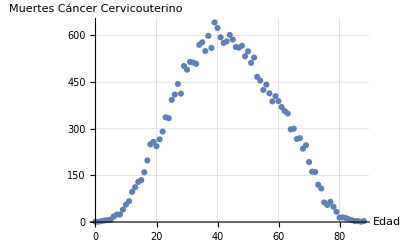

```mathematica
g1=ListPlot[ListaC ,GridLines->Automatic,AxesLabel->{"Edad","Muertes Cáncer Cervicouterino"}]
```

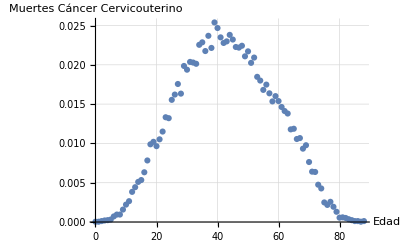

```mathematica
g3=ListPlot[Lista2 ,GridLines->Automatic,AxesLabel->{"Edad","Muertes Cáncer Cervicouterino"}]
```

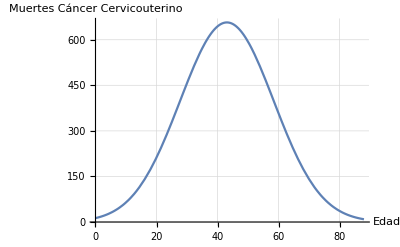

```mathematica
g2=Plot[25285*1/(√(2π)σ) ⅇ^(-(x-μ)^2/(2 σ^2)),{x,0,88},GridLines->Automatic,AxesLabel->{"Edad","Muertes Cáncer Cervicouterino"}]
```

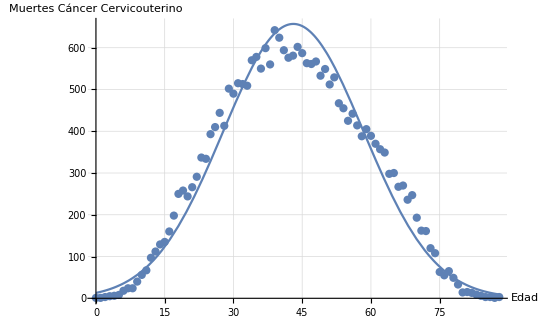

```mathematica
Show[g2,g1]
```